```mathematica
(*----------read the bitstream back from input00----------*)bits=ToExpression/@Characters[Import["input00","Text"]];
Length[bits]

xs=N[Standardize[Take[bits,50000]]];
```

1920192

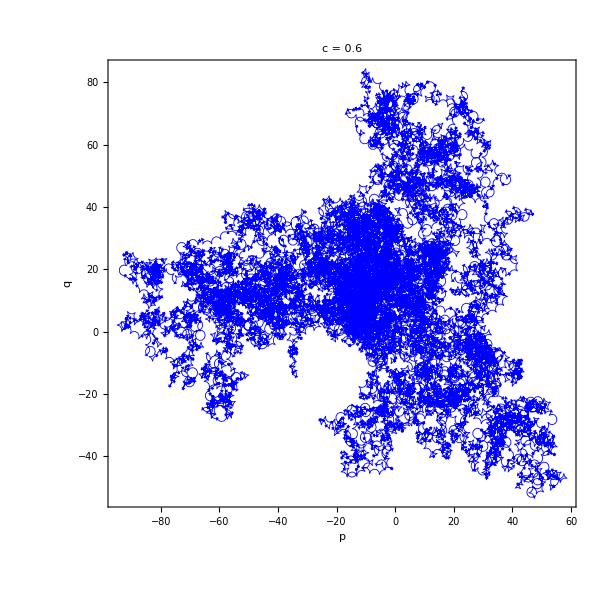

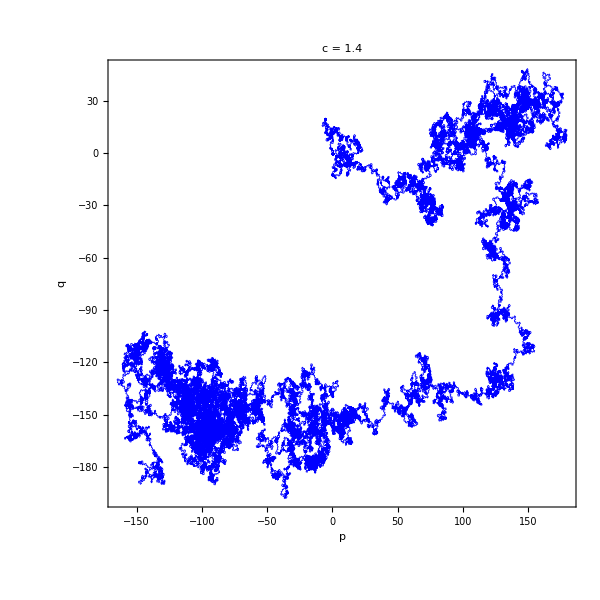

0.997737

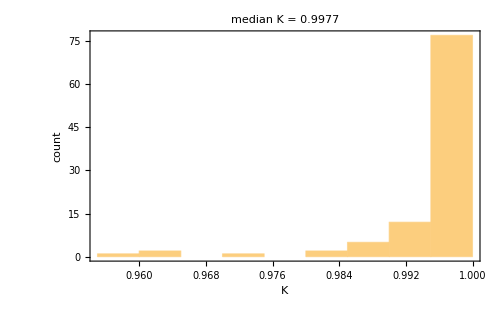

```mathematica
(*----------data----------*)(*5000 points is the right scale for this test;100000 is not*)xs=N[Standardize[Take[key,50000]]];

(*----------p,q----------*)
pq[x_List,c_]:=Module[{n=Length[x]},{Accumulate[x*Cos[c*Range[n]]],Accumulate[x*Sin[c*Range[n]]]}];

(*----------pq plot----------*)
pqPlot[x_List,c_]:=Module[{p,q},{p,q}=pq[x,c];
ListLinePlot[Transpose[{p,q}],PlotStyle->{Blue,Thickness[0.001]},AspectRatio->1,Axes->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["p",Italic,14],Style["q",Italic,14]},ImageSize->600,PlotRangePadding->Scaled[0.05],PlotLabel->Row[{"c = ",c}]]];

pqPlot[xs,0.6]
pqPlot[xs,1.4]

(*----------K statistic----------*)
K01[x_List,c_]:=Module[{n=Length[x],p,q,nMax,M},{p,q}=pq[x,c];
nMax=Floor[n/10];
(*vectorised:Drop replaces the inner loop*)M=Table[Mean[(Drop[p,k]-Drop[p,-k])^2+(Drop[q,k]-Drop[q,-k])^2],{k,1,nMax}];
Correlation[N[Range[nMax]],N[M]]];

cs=RandomReal[{Pi/5,4 Pi/5},100];
Ks=K01[xs,#]&/@cs;
K=Median[Ks]

Histogram[Ks,Automatic,PlotLabel->Row[{"median K = ",NumberForm[K,4]}],FrameLabel->{"K","count"},Frame->True,ImageSize->500]
```